# 1. Numerical Errors

## 1.1 Overflow and Underflow

The following code test overflow and underflow in Mathematica

```mathematica
under = 1.0;
over = 1.0;
n = 1075;
For[i = 0,i<n,i++, 
under/=2;over*=2;Print[i," ",under, " ",over]]
```

0 0.5 2.

1 0.25 4.

2 0.125 8.

3 0.0625 16.

4 0.03125 32.

5 0.015625 64.

6 0.0078125 128.

7 0.00390625 256.

8 0.00195313 512.

9 0.000976563 1024.

10 0.000488281 2048.

11 0.000244141 4096.

12 0.00012207 8192.

13 0.0000610352 16384.

14 0.0000305176 32768.

15 0.0000152588 65536.

16 7.62939×10^-6 131072.

17 3.8147×10^-6 262144.

18 1.90735×10^-6 524288.

19 9.53674×10^-7 1.04858×10^6

20 4.76837×10^-7 2.09715×10^6

21 2.38419×10^-7 4.1943×10^6

22 1.19209×10^-7 8.38861×10^6

23 5.96046×10^-8 1.67772×10^7

24 2.98023×10^-8 3.35544×10^7

25 1.49012×10^-8 6.71089×10^7

26 7.45058×10^-9 1.34218×10^8

27 3.72529×10^-9 2.68435×10^8

28 1.86265×10^-9 5.36871×10^8

29 9.31323×10^-10 1.07374×10^9

30 4.65661×10^-10 2.14748×10^9

31 2.32831×10^-10 4.29497×10^9

32 1.16415×10^-10 8.58993×10^9

33 5.82077×10^-11 1.71799×10^10

34 2.91038×10^-11 3.43597×10^10

35 1.45519×10^-11 6.87195×10^10

36 7.27596×10^-12 1.37439×10^11

37 3.63798×10^-12 2.74878×10^11

38 1.81899×10^-12 5.49756×10^11

39 9.09495×10^-13 1.09951×10^12

40 4.54747×10^-13 2.19902×10^12

41 2.27374×10^-13 4.39805×10^12

42 1.13687×10^-13 8.79609×10^12

43 5.68434×10^-14 1.75922×10^13

44 2.84217×10^-14 3.51844×10^13

45 1.42109×10^-14 7.03687×10^13

46 7.10543×10^-15 1.40737×10^14

47 3.55271×10^-15 2.81475×10^14

48 1.77636×10^-15 5.6295×10^14

49 8.88178×10^-16 1.1259×10^15

50 4.44089×10^-16 2.2518×10^15

51 2.22045×10^-16 4.5036×10^15

52 1.11022×10^-16 9.0072×10^15

53 5.55112×10^-17 1.80144×10^16

54 2.77556×10^-17 3.60288×10^16

55 1.38778×10^-17 7.20576×10^16

56 6.93889×10^-18 1.44115×10^17

57 3.46945×10^-18 2.8823×10^17

58 1.73472×10^-18 5.76461×10^17

59 8.67362×10^-19 1.15292×10^18

60 4.33681×10^-19 2.30584×10^18

61 2.1684×10^-19 4.61169×10^18

62 1.0842×10^-19 9.22337×10^18

63 5.42101×10^-20 1.84467×10^19

64 2.71051×10^-20 3.68935×10^19

65 1.35525×10^-20 7.3787×10^19

66 6.77626×10^-21 1.47574×10^20

67 3.38813×10^-21 2.95148×10^20

68 1.69407×10^-21 5.90296×10^20

69 8.47033×10^-22 1.18059×10^21

70 4.23516×10^-22 2.36118×10^21

71 2.11758×10^-22 4.72237×10^21

72 1.05879×10^-22 9.44473×10^21

73 5.29396×10^-23 1.88895×10^22

74 2.64698×10^-23 3.77789×10^22

75 1.32349×10^-23 7.55579×10^22

76 6.61744×10^-24 1.51116×10^23

77 3.30872×10^-24 3.02231×10^23

78 1.65436×10^-24 6.04463×10^23

79 8.27181×10^-25 1.20893×10^24

80 4.1359×10^-25 2.41785×10^24

81 2.06795×10^-25 4.8357×10^24

82 1.03398×10^-25 9.67141×10^24

83 5.16988×10^-26 1.93428×10^25

84 2.58494×10^-26 3.86856×10^25

85 1.29247×10^-26 7.73713×10^25

86 6.46235×10^-27 1.54743×10^26

87 3.23117×10^-27 3.09485×10^26

88 1.61559×10^-27 6.1897×10^26

89 8.07794×10^-28 1.23794×10^27

90 4.03897×10^-28 2.47588×10^27

91 2.01948×10^-28 4.95176×10^27

92 1.00974×10^-28 9.90352×10^27

93 5.04871×10^-29 1.9807×10^28

94 2.52435×10^-29 3.96141×10^28

95 1.26218×10^-29 7.92282×10^28

96 6.31089×10^-30 1.58456×10^29

97 3.15544×10^-30 3.16913×10^29

98 1.57772×10^-30 6.33825×10^29

99 7.88861×10^-31 1.26765×10^30

100 3.9443×10^-31 2.5353×10^30

101 1.97215×10^-31 5.0706×10^30

102 9.86076×10^-32 1.01412×10^31

103 4.93038×10^-32 2.02824×10^31

104 2.46519×10^-32 4.05648×10^31

105 1.2326×10^-32 8.11296×10^31

106 6.16298×10^-33 1.62259×10^32

107 3.08149×10^-33 3.24519×10^32

108 1.54074×10^-33 6.49037×10^32

109 7.70372×10^-34 1.29807×10^33

110 3.85186×10^-34 2.59615×10^33

111 1.92593×10^-34 5.1923×10^33

112 9.62965×10^-35 1.03846×10^34

113 4.81482×10^-35 2.07692×10^34

114 2.40741×10^-35 4.15384×10^34

115 1.20371×10^-35 8.30767×10^34

116 6.01853×10^-36 1.66153×10^35

117 3.00927×10^-36 3.32307×10^35

118 1.50463×10^-36 6.64614×10^35

119 7.52316×10^-37 1.32923×10^36

120 3.76158×10^-37 2.65846×10^36

121 1.88079×10^-37 5.31691×10^36

122 9.40395×10^-38 1.06338×10^37

123 4.70198×10^-38 2.12676×10^37

124 2.35099×10^-38 4.25353×10^37

125 1.17549×10^-38 8.50706×10^37

126 5.87747×10^-39 1.70141×10^38

127 2.93874×10^-39 3.40282×10^38

128 1.46937×10^-39 6.80565×10^38

129 7.34684×10^-40 1.36113×10^39

130 3.67342×10^-40 2.72226×10^39

131 1.83671×10^-40 5.44452×10^39

132 9.18355×10^-41 1.0889×10^40

133 4.59177×10^-41 2.17781×10^40

134 2.29589×10^-41 4.35561×10^40

135 1.14794×10^-41 8.71123×10^40

136 5.73972×10^-42 1.74225×10^41

137 2.86986×10^-42 3.48449×10^41

138 1.43493×10^-42 6.96898×10^41

139 7.17465×10^-43 1.3938×10^42

140 3.58732×10^-43 2.78759×10^42

141 1.79366×10^-43 5.57519×10^42

142 8.96831×10^-44 1.11504×10^43

143 4.48416×10^-44 2.23007×10^43

144 2.24208×10^-44 4.46015×10^43

145 1.12104×10^-44 8.9203×10^43

146 5.60519×10^-45 1.78406×10^44

147 2.8026×10^-45 3.56812×10^44

148 1.4013×10^-45 7.13624×10^44

149 7.00649×10^-46 1.42725×10^45

150 3.50325×10^-46 2.8545×10^45

151 1.75162×10^-46 5.70899×10^45

152 8.75812×10^-47 1.1418×10^46

153 4.37906×10^-47 2.2836×10^46

154 2.18953×10^-47 4.56719×10^46

155 1.09476×10^-47 9.13439×10^46

156 5.47382×10^-48 1.82688×10^47

157 2.73691×10^-48 3.65375×10^47

158 1.36846×10^-48 7.30751×10^47

159 6.84228×10^-49 1.4615×10^48

160 3.42114×10^-49 2.923×10^48

161 1.71057×10^-49 5.84601×10^48

162 8.55285×10^-50 1.1692×10^49

163 4.27642×10^-50 2.3384×10^49

164 2.13821×10^-50 4.67681×10^49

165 1.06911×10^-50 9.35361×10^49

166 5.34553×10^-51 1.87072×10^50

167 2.67276×10^-51 3.74144×10^50

168 1.33638×10^-51 7.48289×10^50

169 6.68191×10^-52 1.49658×10^51

170 3.34096×10^-52 2.99316×10^51

171 1.67048×10^-52 5.98631×10^51

172 8.35239×10^-53 1.19726×10^52

173 4.17619×10^-53 2.39452×10^52

174 2.0881×10^-53 4.78905×10^52

175 1.04405×10^-53 9.5781×10^52

176 5.22024×10^-54 1.91562×10^53

177 2.61012×10^-54 3.83124×10^53

178 1.30506×10^-54 7.66248×10^53

179 6.5253×10^-55 1.5325×10^54

180 3.26265×10^-55 3.06499×10^54

181 1.63133×10^-55 6.12998×10^54

182 8.15663×10^-56 1.226×10^55

183 4.07832×10^-56 2.45199×10^55

184 2.03916×10^-56 4.90399×10^55

185 1.01958×10^-56 9.80797×10^55

186 5.09789×10^-57 1.96159×10^56

187 2.54895×10^-57 3.92319×10^56

188 1.27447×10^-57 7.84638×10^56

189 6.37237×10^-58 1.56928×10^57

190 3.18618×10^-58 3.13855×10^57

191 1.59309×10^-58 6.2771×10^57

192 7.96546×10^-59 1.25542×10^58

193 3.98273×10^-59 2.51084×10^58

194 1.99136×10^-59 5.02168×10^58

195 9.95682×10^-60 1.00434×10^59

196 4.97841×10^-60 2.00867×10^59

197 2.48921×10^-60 4.01735×10^59

198 1.2446×10^-60 8.03469×10^59

199 6.22302×10^-61 1.60694×10^60

200 3.11151×10^-61 3.21388×10^60

201 1.55575×10^-61 6.42775×10^60

202 7.77877×10^-62 1.28555×10^61

203 3.88938×10^-62 2.5711×10^61

204 1.94469×10^-62 5.1422×10^61

205 9.72346×10^-63 1.02844×10^62

206 4.86173×10^-63 2.05688×10^62

207 2.43087×10^-63 4.11376×10^62

208 1.21543×10^-63 8.22752×10^62

209 6.07716×10^-64 1.6455×10^63

210 3.03858×10^-64 3.29101×10^63

211 1.51929×10^-64 6.58202×10^63

212 7.59645×10^-65 1.3164×10^64

213 3.79823×10^-65 2.63281×10^64

214 1.89911×10^-65 5.26561×10^64

215 9.49557×10^-66 1.05312×10^65

216 4.74778×10^-66 2.10625×10^65

217 2.37389×10^-66 4.21249×10^65

218 1.18695×10^-66 8.42498×10^65

219 5.93473×10^-67 1.685×10^66

220 2.96736×10^-67 3.36999×10^66

221 1.48368×10^-67 6.73999×10^66

222 7.41841×10^-68 1.348×10^67

223 3.70921×10^-68 2.69599×10^67

224 1.8546×10^-68 5.39199×10^67

225 9.27302×10^-69 1.0784×10^68

226 4.63651×10^-69 2.1568×10^68

227 2.31825×10^-69 4.31359×10^68

228 1.15913×10^-69 8.62718×10^68

229 5.79563×10^-70 1.72544×10^69

230 2.89782×10^-70 3.45087×10^69

231 1.44891×10^-70 6.90175×10^69

232 7.24454×10^-71 1.38035×10^70

233 3.62227×10^-71 2.7607×10^70

234 1.81114×10^-71 5.5214×10^70

235 9.05568×10^-72 1.10428×10^71

236 4.52784×10^-72 2.20856×10^71

237 2.26392×10^-72 4.41712×10^71

238 1.13196×10^-72 8.83424×10^71

239 5.6598×10^-73 1.76685×10^72

240 2.8299×10^-73 3.53369×10^72

241 1.41495×10^-73 7.06739×10^72

242 7.07475×10^-74 1.41348×10^73

243 3.53737×10^-74 2.82696×10^73

244 1.76869×10^-74 5.65391×10^73

245 8.84344×10^-75 1.13078×10^74

246 4.42172×10^-75 2.26156×10^74

247 2.21086×10^-75 4.52313×10^74

248 1.10543×10^-75 9.04626×10^74

249 5.52715×10^-76 1.80925×10^75

250 2.76357×10^-76 3.6185×10^75

251 1.38179×10^-76 7.23701×10^75

252 6.90893×10^-77 1.4474×10^76

253 3.45447×10^-77 2.8948×10^76

254 1.72723×10^-77 5.7896×10^76

255 8.63617×10^-78 1.15792×10^77

256 4.31808×10^-78 2.31584×10^77

257 2.15904×10^-78 4.63168×10^77

258 1.07952×10^-78 9.26337×10^77

259 5.39761×10^-79 1.85267×10^78

260 2.6988×10^-79 3.70535×10^78

261 1.3494×10^-79 7.41069×10^78

262 6.74701×10^-80 1.48214×10^79

263 3.3735×10^-80 2.96428×10^79

264 1.68675×10^-80 5.92855×10^79

265 8.43376×10^-81 1.18571×10^80

266 4.21688×10^-81 2.37142×10^80

267 2.10844×10^-81 4.74284×10^80

268 1.05422×10^-81 9.48569×10^80

269 5.2711×10^-82 1.89714×10^81

270 2.63555×10^-82 3.79428×10^81

271 1.31777×10^-82 7.58855×10^81

272 6.58887×10^-83 1.51771×10^82

273 3.29444×10^-83 3.03542×10^82

274 1.64722×10^-83 6.07084×10^82

275 8.23609×10^-84 1.21417×10^83

276 4.11805×10^-84 2.42834×10^83

277 2.05902×10^-84 4.85667×10^83

278 1.02951×10^-84 9.71334×10^83

279 5.14756×10^-85 1.94267×10^84

280 2.57378×10^-85 3.88534×10^84

281 1.28689×10^-85 7.77068×10^84

282 6.43445×10^-86 1.55414×10^85

283 3.21722×10^-86 3.10827×10^85

284 1.60861×10^-86 6.21654×10^85

285 8.04306×10^-87 1.24331×10^86

286 4.02153×10^-87 2.48662×10^86

287 2.01076×10^-87 4.97323×10^86

288 1.00538×10^-87 9.94646×10^86

289 5.02691×10^-88 1.98929×10^87

290 2.51346×10^-88 3.97859×10^87

291 1.25673×10^-88 7.95717×10^87

292 6.28364×10^-89 1.59143×10^88

293 3.14182×10^-89 3.18287×10^88

294 1.57091×10^-89 6.36574×10^88

295 7.85455×10^-90 1.27315×10^89

296 3.92727×10^-90 2.54629×10^89

297 1.96364×10^-90 5.09259×10^89

298 9.81819×10^-91 1.01852×10^90

299 4.90909×10^-91 2.03704×10^90

300 2.45455×10^-91 4.07407×10^90

301 1.22727×10^-91 8.14814×10^90

302 6.13637×10^-92 1.62963×10^91

303 3.06818×10^-92 3.25926×10^91

304 1.53409×10^-92 6.51852×10^91

305 7.67046×10^-93 1.3037×10^92

306 3.83523×10^-93 2.60741×10^92

307 1.91761×10^-93 5.21481×10^92

308 9.58807×10^-94 1.04296×10^93

309 4.79404×10^-94 2.08592×10^93

310 2.39702×10^-94 4.17185×10^93

311 1.19851×10^-94 8.3437×10^93

312 5.99255×10^-95 1.66874×10^94

313 2.99627×10^-95 3.33748×10^94

314 1.49814×10^-95 6.67496×10^94

315 7.49068×10^-96 1.33499×10^95

316 3.74534×10^-96 2.66998×10^95

317 1.87267×10^-96 5.33997×10^95

318 9.36335×10^-97 1.06799×10^96

319 4.68168×10^-97 2.13599×10^96

320 2.34084×10^-97 4.27197×10^96

321 1.17042×10^-97 8.54395×10^96

322 5.8521×10^-98 1.70879×10^97

323 2.92605×10^-98 3.41758×10^97

324 1.46302×10^-98 6.83516×10^97

325 7.31512×10^-99 1.36703×10^98

326 3.65756×10^-99 2.73406×10^98

327 1.82878×10^-99 5.46813×10^98

328 9.1439×10^-100 1.09363×10^99

329 4.57195×10^-100 2.18725×10^99

330 2.28597×10^-100 4.3745×10^99

331 1.14299×10^-100 8.749×10^99

332 5.71494×10^-101 1.7498×10^100

333 2.85747×10^-101 3.4996×10^100

334 1.42873×10^-101 6.9992×10^100

335 7.14367×10^-102 1.39984×10^101

336 3.57184×10^-102 2.79968×10^101

337 1.78592×10^-102 5.59936×10^101

338 8.92959×10^-103 1.11987×10^102

339 4.46479×10^-103 2.23974×10^102

340 2.2324×10^-103 4.47949×10^102

341 1.1162×10^-103 8.95898×10^102

342 5.58099×10^-104 1.7918×10^103

343 2.7905×10^-104 3.58359×10^103

344 1.39525×10^-104 7.16718×10^103

345 6.97624×10^-105 1.43344×10^104

346 3.48812×10^-105 2.86687×10^104

347 1.74406×10^-105 5.73375×10^104

348 8.7203×10^-106 1.14675×10^105

349 4.36015×10^-106 2.2935×10^105

350 2.18008×10^-106 4.587×10^105

351 1.09004×10^-106 9.17399×10^105

352 5.45019×10^-107 1.8348×10^106

353 2.72509×10^-107 3.6696×10^106

354 1.36255×10^-107 7.3392×10^106

355 6.81274×10^-108 1.46784×10^107

356 3.40637×10^-108 2.93568×10^107

357 1.70318×10^-108 5.87136×10^107

358 8.51592×10^-109 1.17427×10^108

359 4.25796×10^-109 2.34854×10^108

360 2.12898×10^-109 4.69709×10^108

361 1.06449×10^-109 9.39417×10^108

362 5.32245×10^-110 1.87883×10^109

363 2.66122×10^-110 3.75767×10^109

364 1.33061×10^-110 7.51534×10^109

365 6.65306×10^-111 1.50307×10^110

366 3.32653×10^-111 3.00613×10^110

367 1.66327×10^-111 6.01227×10^110

368 8.31633×10^-112 1.20245×10^111

369 4.15816×10^-112 2.40491×10^111

370 2.07908×10^-112 4.80982×10^111

371 1.03954×10^-112 9.61963×10^111

372 5.1977×10^-113 1.92393×10^112

373 2.59885×10^-113 3.84785×10^112

374 1.29943×10^-113 7.6957×10^112

375 6.49713×10^-114 1.53914×10^113

376 3.24857×10^-114 3.07828×10^113

377 1.62428×10^-114 6.15656×10^113

378 8.12141×10^-115 1.23131×10^114

379 4.06071×10^-115 2.46263×10^114

380 2.03035×10^-115 4.92525×10^114

381 1.01518×10^-115 9.8505×10^114

382 5.07588×10^-116 1.9701×10^115

383 2.53794×10^-116 3.9402×10^115

384 1.26897×10^-116 7.8804×10^115

385 6.34485×10^-117 1.57608×10^116

386 3.17243×10^-117 3.15216×10^116

387 1.58621×10^-117 6.30432×10^116

388 7.93107×10^-118 1.26086×10^117

389 3.96553×10^-118 2.52173×10^117

390 1.98277×10^-118 5.04346×10^117

391 9.91384×10^-119 1.00869×10^118

392 4.95692×10^-119 2.01738×10^118

393 2.47846×10^-119 4.03477×10^118

394 1.23923×10^-119 8.06953×10^118

395 6.19615×10^-120 1.61391×10^119

396 3.09807×10^-120 3.22781×10^119

397 1.54904×10^-120 6.45562×10^119

398 7.74518×10^-121 1.29112×10^120

399 3.87259×10^-121 2.58225×10^120

400 1.9363×10^-121 5.1645×10^120

401 9.68148×10^-122 1.0329×10^121

402 4.84074×10^-122 2.0658×10^121

403 2.42037×10^-122 4.1316×10^121

404 1.21018×10^-122 8.2632×10^121

405 6.05092×10^-123 1.65264×10^122

406 3.02546×10^-123 3.30528×10^122

407 1.51273×10^-123 6.61056×10^122

408 7.56366×10^-124 1.32211×10^123

409 3.78183×10^-124 2.64422×10^123

410 1.89091×10^-124 5.28845×10^123

411 9.45457×10^-125 1.05769×10^124

412 4.72729×10^-125 2.11538×10^124

413 2.36364×10^-125 4.23076×10^124

414 1.18182×10^-125 8.46152×10^124

415 5.90911×10^-126 1.6923×10^125

416 2.95455×10^-126 3.38461×10^125

417 1.47728×10^-126 6.76921×10^125

418 7.38638×10^-127 1.35384×10^126

419 3.69319×10^-127 2.70769×10^126

420 1.8466×10^-127 5.41537×10^126

421 9.23298×10^-128 1.08307×10^127

422 4.61649×10^-128 2.16615×10^127

423 2.30824×10^-128 4.3323×10^127

424 1.15412×10^-128 8.66459×10^127

425 5.77061×10^-129 1.73292×10^128

426 2.88531×10^-129 3.46584×10^128

427 1.44265×10^-129 6.93167×10^128

428 7.21326×10^-130 1.38633×10^129

429 3.60663×10^-130 2.77267×10^129

430 1.80332×10^-130 5.54534×10^129

431 9.01658×10^-131 1.10907×10^130

432 4.50829×10^-131 2.21814×10^130

433 2.25415×10^-131 4.43627×10^130

434 1.12707×10^-131 8.87254×10^130

435 5.63536×10^-132 1.77451×10^131

436 2.81768×10^-132 3.54902×10^131

437 1.40884×10^-132 7.09803×10^131

438 7.0442×10^-133 1.41961×10^132

439 3.5221×10^-133 2.83921×10^132

440 1.76105×10^-133 5.67843×10^132

441 8.80525×10^-134 1.13569×10^133

442 4.40263×10^-134 2.27137×10^133

443 2.20131×10^-134 4.54274×10^133

444 1.10066×10^-134 9.08548×10^133

445 5.50328×10^-135 1.8171×10^134

446 2.75164×10^-135 3.63419×10^134

447 1.37582×10^-135 7.26839×10^134

448 6.87911×10^-136 1.45368×10^135

449 3.43955×10^-136 2.90735×10^135

450 1.71978×10^-136 5.81471×10^135

451 8.59888×10^-137 1.16294×10^136

452 4.29944×10^-137 2.32588×10^136

453 2.14972×10^-137 4.65177×10^136

454 1.07486×10^-137 9.30354×10^136

455 5.3743×10^-138 1.86071×10^137

456 2.68715×10^-138 3.72141×10^137

457 1.34358×10^-138 7.44283×10^137

458 6.71788×10^-139 1.48857×10^138

459 3.35894×10^-139 2.97713×10^138

460 1.67947×10^-139 5.95426×10^138

461 8.39735×10^-140 1.19085×10^139

462 4.19867×10^-140 2.38171×10^139

463 2.09934×10^-140 4.76341×10^139

464 1.04967×10^-140 9.52682×10^139

465 5.24834×10^-141 1.90536×10^140

466 2.62417×10^-141 3.81073×10^140

467 1.31209×10^-141 7.62146×10^140

468 6.56043×10^-142 1.52429×10^141

469 3.28021×10^-142 3.04858×10^141

470 1.64011×10^-142 6.09717×10^141

471 8.20053×10^-143 1.21943×10^142

472 4.10027×10^-143 2.43887×10^142

473 2.05013×10^-143 4.87773×10^142

474 1.02507×10^-143 9.75546×10^142

475 5.12533×10^-144 1.95109×10^143

476 2.56267×10^-144 3.90219×10^143

477 1.28133×10^-144 7.80437×10^143

478 6.40667×10^-145 1.56087×10^144

479 3.20333×10^-145 3.12175×10^144

480 1.60167×10^-145 6.2435×10^144

481 8.00833×10^-146 1.2487×10^145

482 4.00417×10^-146 2.4974×10^145

483 2.00208×10^-146 4.9948×10^145

484 1.00104×10^-146 9.9896×10^145

485 5.00521×10^-147 1.99792×10^146

486 2.5026×10^-147 3.99584×10^146

487 1.2513×10^-147 7.99168×10^146

488 6.25651×10^-148 1.59834×10^147

489 3.12825×10^-148 3.19667×10^147

490 1.56413×10^-148 6.39334×10^147

491 7.82064×10^-149 1.27867×10^148

492 3.91032×10^-149 2.55734×10^148

493 1.95516×10^-149 5.11467×10^148

494 9.7758×10^-150 1.02293×10^149

495 4.8879×10^-150 2.04587×10^149

496 2.44395×10^-150 4.09174×10^149

497 1.22197×10^-150 8.18348×10^149

498 6.10987×10^-151 1.6367×10^150

499 3.05494×10^-151 3.27339×10^150

500 1.52747×10^-151 6.54678×10^150

501 7.63734×10^-152 1.30936×10^151

502 3.81867×10^-152 2.61871×10^151

503 1.90934×10^-152 5.23742×10^151

504 9.54668×10^-153 1.04748×10^152

505 4.77334×10^-153 2.09497×10^152

506 2.38667×10^-153 4.18994×10^152

507 1.19333×10^-153 8.37988×10^152

508 5.96667×10^-154 1.67598×10^153

509 2.98334×10^-154 3.35195×10^153

510 1.49167×10^-154 6.7039×10^153

511 7.45834×10^-155 1.34078×10^154

512 3.72917×10^-155 2.68156×10^154

513 1.86459×10^-155 5.36312×10^154

514 9.32293×10^-156 1.07262×10^155

515 4.66146×10^-156 2.14525×10^155

516 2.33073×10^-156 4.2905×10^155

517 1.16537×10^-156 8.581×10^155

518 5.82683×10^-157 1.7162×10^156

519 2.91341×10^-157 3.4324×10^156

520 1.45671×10^-157 6.8648×10^156

521 7.28354×10^-158 1.37296×10^157

522 3.64177×10^-158 2.74592×10^157

523 1.82088×10^-158 5.49184×10^157

524 9.10442×10^-159 1.09837×10^158

525 4.55221×10^-159 2.19674×10^158

526 2.2761×10^-159 4.39347×10^158

527 1.13805×10^-159 8.78694×10^158

528 5.69026×10^-160 1.75739×10^159

529 2.84513×10^-160 3.51478×10^159

530 1.42257×10^-160 7.02955×10^159

531 7.11283×10^-161 1.40591×10^160

532 3.55641×10^-161 2.81182×10^160

533 1.77821×10^-161 5.62364×10^160

534 8.89103×10^-162 1.12473×10^161

535 4.44552×10^-162 2.24946×10^161

536 2.22276×10^-162 4.49891×10^161

537 1.11138×10^-162 8.99783×10^161

538 5.5569×10^-163 1.79957×10^162

539 2.77845×10^-163 3.59913×10^162

540 1.38922×10^-163 7.19826×10^162

541 6.94612×10^-164 1.43965×10^163

542 3.47306×10^-164 2.8793×10^163

543 1.73653×10^-164 5.75861×10^163

544 8.68265×10^-165 1.15172×10^164

545 4.34133×10^-165 2.30344×10^164

546 2.17066×10^-165 4.60689×10^164

547 1.08533×10^-165 9.21378×10^164

548 5.42666×10^-166 1.84276×10^165

549 2.71333×10^-166 3.68551×10^165

550 1.35666×10^-166 7.37102×10^165

551 6.78332×10^-167 1.4742×10^166

552 3.39166×10^-167 2.94841×10^166

553 1.69583×10^-167 5.89682×10^166

554 8.47915×10^-168 1.17936×10^167

555 4.23958×10^-168 2.35873×10^167

556 2.11979×10^-168 4.71745×10^167

557 1.05989×10^-168 9.43491×10^167

558 5.29947×10^-169 1.88698×10^168

559 2.64973×10^-169 3.77396×10^168

560 1.32487×10^-169 7.54792×10^168

561 6.62434×10^-170 1.50958×10^169

562 3.31217×10^-170 3.01917×10^169

563 1.65608×10^-170 6.03834×10^169

564 8.28042×10^-171 1.20767×10^170

565 4.14021×10^-171 2.41534×10^170

566 2.07011×10^-171 4.83067×10^170

567 1.03505×10^-171 9.66134×10^170

568 5.17526×10^-172 1.93227×10^171

569 2.58763×10^-172 3.86454×10^171

570 1.29382×10^-172 7.72908×10^171

571 6.46908×10^-173 1.54582×10^172

572 3.23454×10^-173 3.09163×10^172

573 1.61727×10^-173 6.18326×10^172

574 8.08635×10^-174 1.23665×10^173

575 4.04317×10^-174 2.4733×10^173

576 2.02159×10^-174 4.94661×10^173

577 1.01079×10^-174 9.89322×10^173

578 5.05397×10^-175 1.97864×10^174

579 2.52698×10^-175 3.95729×10^174

580 1.26349×10^-175 7.91457×10^174

581 6.31746×10^-176 1.58291×10^175

582 3.15873×10^-176 3.16583×10^175

583 1.57937×10^-176 6.33166×10^175

584 7.89683×10^-177 1.26633×10^176

585 3.94841×10^-177 2.53266×10^176

586 1.97421×10^-177 5.06533×10^176

587 9.87103×10^-178 1.01307×10^177

588 4.93552×10^-178 2.02613×10^177

589 2.46776×10^-178 4.05226×10^177

590 1.23388×10^-178 8.10452×10^177

591 6.16939×10^-179 1.6209×10^178

592 3.0847×10^-179 3.24181×10^178

593 1.54235×10^-179 6.48362×10^178

594 7.71174×10^-180 1.29672×10^179

595 3.85587×10^-180 2.59345×10^179

596 1.92794×10^-180 5.18689×10^179

597 9.63968×10^-181 1.03738×10^180

598 4.81984×10^-181 2.07476×10^180

599 2.40992×10^-181 4.14952×10^180

600 1.20496×10^-181 8.29903×10^180

601 6.0248×10^-182 1.65981×10^181

602 3.0124×10^-182 3.31961×10^181

603 1.5062×10^-182 6.63922×10^181

604 7.531×10^-183 1.32784×10^182

605 3.7655×10^-183 2.65569×10^182

606 1.88275×10^-183 5.31138×10^182

607 9.41375×10^-184 1.06228×10^183

608 4.70687×10^-184 2.12455×10^183

609 2.35344×10^-184 4.2491×10^183

610 1.17672×10^-184 8.49821×10^183

611 5.88359×10^-185 1.69964×10^184

612 2.9418×10^-185 3.39928×10^184

613 1.4709×10^-185 6.79857×10^184

614 7.35449×10^-186 1.35971×10^185

615 3.67725×10^-186 2.71943×10^185

616 1.83862×10^-186 5.43885×10^185

617 9.19311×10^-187 1.08777×10^186

618 4.59656×10^-187 2.17554×10^186

619 2.29828×10^-187 4.35108×10^186

620 1.14914×10^-187 8.70216×10^186

621 5.7457×10^-188 1.74043×10^187

622 2.87285×10^-188 3.48087×10^187

623 1.43642×10^-188 6.96173×10^187

624 7.18212×10^-189 1.39235×10^188

625 3.59106×10^-189 2.78469×10^188

626 1.79553×10^-189 5.56939×10^188

627 8.97765×10^-190 1.11388×10^189

628 4.48883×10^-190 2.22775×10^189

629 2.24441×10^-190 4.45551×10^189

630 1.12221×10^-190 8.91102×10^189

631 5.61103×10^-191 1.7822×10^190

632 2.80552×10^-191 3.56441×10^190

633 1.40276×10^-191 7.12881×10^190

634 7.01379×10^-192 1.42576×10^191

635 3.50689×10^-192 2.85153×10^191

636 1.75345×10^-192 5.70305×10^191

637 8.76724×10^-193 1.14061×10^192

638 4.38362×10^-193 2.28122×10^192

639 2.19181×10^-193 4.56244×10^192

640 1.0959×10^-193 9.12488×10^192

641 5.47952×10^-194 1.82498×10^193

642 2.73976×10^-194 3.64995×10^193

643 1.36988×10^-194 7.2999×10^193

644 6.8494×10^-195 1.45998×10^194

645 3.4247×10^-195 2.91996×10^194

646 1.71235×10^-195 5.83992×10^194

647 8.56176×10^-196 1.16798×10^195

648 4.28088×10^-196 2.33597×10^195

649 2.14044×10^-196 4.67194×10^195

650 1.07022×10^-196 9.34388×10^195

651 5.3511×10^-197 1.86878×10^196

652 2.67555×10^-197 3.73755×10^196

653 1.33777×10^-197 7.4751×10^196

654 6.68887×10^-198 1.49502×10^197

655 3.34444×10^-198 2.99004×10^197

656 1.67222×10^-198 5.98008×10^197

657 8.36109×10^-199 1.19602×10^198

658 4.18054×10^-199 2.39203×10^198

659 2.09027×10^-199 4.78407×10^198

660 1.04514×10^-199 9.56813×10^198

661 5.22568×10^-200 1.91363×10^199

662 2.61284×10^-200 3.82725×10^199

663 1.30642×10^-200 7.65451×10^199

664 6.5321×10^-201 1.5309×10^200

665 3.26605×10^-201 3.0618×10^200

666 1.63303×10^-201 6.1236×10^200

667 8.16513×10^-202 1.22472×10^201

668 4.08256×10^-202 2.44944×10^201

669 2.04128×10^-202 4.89888×10^201

670 1.02064×10^-202 9.79777×10^201

671 5.1032×10^-203 1.95955×10^202

672 2.5516×10^-203 3.91911×10^202

673 1.2758×10^-203 7.83821×10^202

674 6.379×10^-204 1.56764×10^203

675 3.1895×10^-204 3.13529×10^203

676 1.59475×10^-204 6.27057×10^203

677 7.97376×10^-205 1.25411×10^204

678 3.98688×10^-205 2.50823×10^204

679 1.99344×10^-205 5.01646×10^204

680 9.96719×10^-206 1.00329×10^205

681 4.9836×10^-206 2.00658×10^205

682 2.4918×10^-206 4.01317×10^205

683 1.2459×10^-206 8.02633×10^205

684 6.2295×10^-207 1.60527×10^206

685 3.11475×10^-207 3.21053×10^206

686 1.55737×10^-207 6.42106×10^206

687 7.78687×10^-208 1.28421×10^207

688 3.89344×10^-208 2.56843×10^207

689 1.94672×10^-208 5.13685×10^207

690 9.73359×10^-209 1.02737×10^208

691 4.86679×10^-209 2.05474×10^208

692 2.4334×10^-209 4.10948×10^208

693 1.2167×10^-209 8.21896×10^208

694 6.08349×10^-210 1.64379×10^209

695 3.04175×10^-210 3.28758×10^209

696 1.52087×10^-210 6.57517×10^209

697 7.60437×10^-211 1.31503×10^210

698 3.80218×10^-211 2.63007×10^210

699 1.90109×10^-211 5.26014×10^210

700 9.50546×10^-212 1.05203×10^211

701 4.75273×10^-212 2.10405×10^211

702 2.37636×10^-212 4.20811×10^211

703 1.18818×10^-212 8.41622×10^211

704 5.94091×10^-213 1.68324×10^212

705 2.97046×10^-213 3.36649×10^212

706 1.48523×10^-213 6.73297×10^212

707 7.42614×10^-214 1.34659×10^213

708 3.71307×10^-214 2.69319×10^213

709 1.85653×10^-214 5.38638×10^213

710 9.28267×10^-215 1.07728×10^214

711 4.64134×10^-215 2.15455×10^214

712 2.32067×10^-215 4.3091×10^214

713 1.16033×10^-215 8.61821×10^214

714 5.80167×10^-216 1.72364×10^215

715 2.90084×10^-216 3.44728×10^215

716 1.45042×10^-216 6.89457×10^215

717 7.25209×10^-217 1.37891×10^216

718 3.62604×10^-217 2.75783×10^216

719 1.81302×10^-217 5.51565×10^216

720 9.06511×10^-218 1.10313×10^217

721 4.53256×10^-218 2.20626×10^217

722 2.26628×10^-218 4.41252×10^217

723 1.13314×10^-218 8.82504×10^217

724 5.66569×10^-219 1.76501×10^218

725 2.83285×10^-219 3.53002×10^218

726 1.41642×10^-219 7.06003×10^218

727 7.08212×10^-220 1.41201×10^219

728 3.54106×10^-220 2.82401×10^219

729 1.77053×10^-220 5.64803×10^219

730 8.85265×10^-221 1.12961×10^220

731 4.42632×10^-221 2.25921×10^220

732 2.21316×10^-221 4.51842×10^220

733 1.10658×10^-221 9.03684×10^220

734 5.5329×10^-222 1.80737×10^221

735 2.76645×10^-222 3.61474×10^221

736 1.38323×10^-222 7.22948×10^221

737 6.91613×10^-223 1.4459×10^222

738 3.45807×10^-223 2.89179×10^222

739 1.72903×10^-223 5.78358×10^222

740 8.64516×10^-224 1.15672×10^223

741 4.32258×10^-224 2.31343×10^223

742 2.16129×10^-224 4.62686×10^223

743 1.08065×10^-224 9.25373×10^223

744 5.40323×10^-225 1.85075×10^224

745 2.70161×10^-225 3.70149×10^224

746 1.35081×10^-225 7.40298×10^224

747 6.75403×10^-226 1.4806×10^225

748 3.37702×10^-226 2.96119×10^225

749 1.68851×10^-226 5.92239×10^225

750 8.44254×10^-227 1.18448×10^226

751 4.22127×10^-227 2.36895×10^226

752 2.11064×10^-227 4.73791×10^226

753 1.05532×10^-227 9.47582×10^226

754 5.27659×10^-228 1.89516×10^227

755 2.63829×10^-228 3.79033×10^227

756 1.31915×10^-228 7.58065×10^227

757 6.59574×10^-229 1.51613×10^228

758 3.29787×10^-229 3.03226×10^228

759 1.64893×10^-229 6.06452×10^228

760 8.24467×10^-230 1.2129×10^229

761 4.12234×10^-230 2.42581×10^229

762 2.06117×10^-230 4.85162×10^229

763 1.03058×10^-230 9.70324×10^229

764 5.15292×10^-231 1.94065×10^230

765 2.57646×10^-231 3.8813×10^230

766 1.28823×10^-231 7.76259×10^230

767 6.44115×10^-232 1.55252×10^231

768 3.22057×10^-232 3.10504×10^231

769 1.61029×10^-232 6.21007×10^231

770 8.05144×10^-233 1.24201×10^232

771 4.02572×10^-233 2.48403×10^232

772 2.01286×10^-233 4.96806×10^232

773 1.00643×10^-233 9.93612×10^232

774 5.03215×10^-234 1.98722×10^233

775 2.51607×10^-234 3.97445×10^233

776 1.25804×10^-234 7.94889×10^233

777 6.29018×10^-235 1.58978×10^234

778 3.14509×10^-235 3.17956×10^234

779 1.57255×10^-235 6.35911×10^234

780 7.86273×10^-236 1.27182×10^235

781 3.93137×10^-236 2.54365×10^235

782 1.96568×10^-236 5.08729×10^235

783 9.82841×10^-237 1.01746×10^236

784 4.91421×10^-237 2.03492×10^236

785 2.4571×10^-237 4.06983×10^236

786 1.22855×10^-237 8.13967×10^236

787 6.14276×10^-238 1.62793×10^237

788 3.07138×10^-238 3.25587×10^237

789 1.53569×10^-238 6.51173×10^237

790 7.67845×10^-239 1.30235×10^238

791 3.83922×10^-239 2.60469×10^238

792 1.91961×10^-239 5.20939×10^238

793 9.59806×10^-240 1.04188×10^239

794 4.79903×10^-240 2.08375×10^239

795 2.39951×10^-240 4.16751×10^239

796 1.19976×10^-240 8.33502×10^239

797 5.99879×10^-241 1.667×10^240

798 2.99939×10^-241 3.33401×10^240

799 1.4997×10^-241 6.66801×10^240

800 7.49848×10^-242 1.3336×10^241

801 3.74924×10^-242 2.66721×10^241

802 1.87462×10^-242 5.33441×10^241

803 9.37311×10^-243 1.06688×10^242

804 4.68655×10^-243 2.13376×10^242

805 2.34328×10^-243 4.26753×10^242

806 1.17164×10^-243 8.53506×10^242

807 5.85819×10^-244 1.70701×10^243

808 2.9291×10^-244 3.41402×10^243

809 1.46455×10^-244 6.82805×10^243

810 7.32274×10^-245 1.36561×10^244

811 3.66137×10^-245 2.73122×10^244

812 1.83068×10^-245 5.46244×10^244

813 9.15342×10^-246 1.09249×10^245

814 4.57671×10^-246 2.18497×10^245

815 2.28836×10^-246 4.36995×10^245

816 1.14418×10^-246 8.7399×10^245

817 5.72089×10^-247 1.74798×10^246

818 2.86044×10^-247 3.49596×10^246

819 1.43022×10^-247 6.99192×10^246

820 7.15111×10^-248 1.39838×10^247

821 3.57556×10^-248 2.79677×10^247

822 1.78778×10^-248 5.59354×10^247

823 8.93889×10^-249 1.11871×10^248

824 4.46944×10^-249 2.23741×10^248

825 2.23472×10^-249 4.47483×10^248

826 1.11736×10^-249 8.94966×10^248

827 5.58681×10^-250 1.78993×10^249

828 2.7934×10^-250 3.57986×10^249

829 1.3967×10^-250 7.15973×10^249

830 6.98351×10^-251 1.43195×10^250

831 3.49175×10^-251 2.86389×10^250

832 1.74588×10^-251 5.72778×10^250

833 8.72938×10^-252 1.14556×10^251

834 4.36469×10^-252 2.29111×10^251

835 2.18235×10^-252 4.58222×10^251

836 1.09117×10^-252 9.16445×10^251

837 5.45587×10^-253 1.83289×10^252

838 2.72793×10^-253 3.66578×10^252

839 1.36397×10^-253 7.33156×10^252

840 6.81983×10^-254 1.46631×10^253

841 3.40992×10^-254 2.93262×10^253

842 1.70496×10^-254 5.86525×10^253

843 8.52479×10^-255 1.17305×10^254

844 4.26239×10^-255 2.3461×10^254

845 2.1312×10^-255 4.6922×10^254

846 1.0656×10^-255 9.3844×10^254

847 5.32799×10^-256 1.87688×10^255

848 2.664×10^-256 3.75376×10^255

849 1.332×10^-256 7.50752×10^255

850 6.65999×10^-257 1.5015×10^256

851 3.33×10^-257 3.00301×10^256

852 1.665×10^-257 6.00601×10^256

853 8.32499×10^-258 1.2012×10^257

854 4.16249×10^-258 2.40241×10^257

855 2.08125×10^-258 4.80481×10^257

856 1.04062×10^-258 9.60962×10^257

857 5.20312×10^-259 1.92192×10^258

858 2.60156×10^-259 3.84385×10^258

859 1.30078×10^-259 7.6877×10^258

860 6.5039×10^-260 1.53754×10^259

861 3.25195×10^-260 3.07508×10^259

862 1.62597×10^-260 6.15016×10^259

863 8.12987×10^-261 1.23003×10^260

864 4.06494×10^-261 2.46006×10^260

865 2.03247×10^-261 4.92013×10^260

866 1.01623×10^-261 9.84025×10^260

867 5.08117×10^-262 1.96805×10^261

868 2.54059×10^-262 3.9361×10^261

869 1.27029×10^-262 7.8722×10^261

870 6.35146×10^-263 1.57444×10^262

871 3.17573×10^-263 3.14888×10^262

872 1.58787×10^-263 6.29776×10^262

873 7.93933×10^-264 1.25955×10^263

874 3.96966×10^-264 2.5191×10^263

875 1.98483×10^-264 5.03821×10^263

876 9.92416×10^-265 1.00764×10^264

877 4.96208×10^-265 2.01528×10^264

878 2.48104×10^-265 4.03057×10^264

879 1.24052×10^-265 8.06113×10^264

880 6.2026×10^-266 1.61223×10^265

881 3.1013×10^-266 3.22445×10^265

882 1.55065×10^-266 6.44891×10^265

883 7.75325×10^-267 1.28978×10^266

884 3.87663×10^-267 2.57956×10^266

885 1.93831×10^-267 5.15913×10^266

886 9.69156×10^-268 1.03183×10^267

887 4.84578×10^-268 2.06365×10^267

888 2.42289×10^-268 4.1273×10^267

889 1.21145×10^-268 8.2546×10^267

890 6.05723×10^-269 1.65092×10^268

891 3.02861×10^-269 3.30184×10^268

892 1.51431×10^-269 6.60368×10^268

893 7.57153×10^-270 1.32074×10^269

894 3.78577×10^-270 2.64147×10^269

895 1.89288×10^-270 5.28295×10^269

896 9.46442×10^-271 1.05659×10^270

897 4.73221×10^-271 2.11318×10^270

898 2.3661×10^-271 4.22636×10^270

899 1.18305×10^-271 8.45271×10^270

900 5.91526×10^-272 1.69054×10^271

901 2.95763×10^-272 3.38108×10^271

902 1.47882×10^-272 6.76217×10^271

903 7.39408×10^-273 1.35243×10^272

904 3.69704×10^-273 2.70487×10^272

905 1.84852×10^-273 5.40974×10^272

906 9.2426×10^-274 1.08195×10^273

907 4.6213×10^-274 2.16389×10^273

908 2.31065×10^-274 4.32779×10^273

909 1.15532×10^-274 8.65558×10^273

910 5.77662×10^-275 1.73112×10^274

911 2.88831×10^-275 3.46223×10^274

912 1.44416×10^-275 6.92446×10^274

913 7.22078×10^-276 1.38489×10^275

914 3.61039×10^-276 2.76978×10^275

915 1.80519×10^-276 5.53957×10^275

916 9.02597×10^-277 1.10791×10^276

917 4.51299×10^-277 2.21583×10^276

918 2.25649×10^-277 4.43166×10^276

919 1.12825×10^-277 8.86331×10^276

920 5.64123×10^-278 1.77266×10^277

921 2.82062×10^-278 3.54532×10^277

922 1.41031×10^-278 7.09065×10^277

923 7.05154×10^-279 1.41813×10^278

924 3.52577×10^-279 2.83626×10^278

925 1.76289×10^-279 5.67252×10^278

926 8.81443×10^-280 1.1345×10^279

927 4.40721×10^-280 2.26901×10^279

928 2.20361×10^-280 4.53802×10^279

929 1.1018×10^-280 9.07603×10^279

930 5.50902×10^-281 1.81521×10^280

931 2.75451×10^-281 3.63041×10^280

932 1.37725×10^-281 7.26082×10^280

933 6.88627×10^-282 1.45216×10^281

934 3.44314×10^-282 2.90433×10^281

935 1.72157×10^-282 5.80866×10^281

936 8.60784×10^-283 1.16173×10^282

937 4.30392×10^-283 2.32346×10^282

938 2.15196×10^-283 4.64693×10^282

939 1.07598×10^-283 9.29386×10^282

940 5.3799×10^-284 1.85877×10^283

941 2.68995×10^-284 3.71754×10^283

942 1.34497×10^-284 7.43508×10^283

943 6.72487×10^-285 1.48702×10^284

944 3.36244×10^-285 2.97403×10^284

945 1.68122×10^-285 5.94807×10^284

946 8.40609×10^-286 1.18961×10^285

947 4.20305×10^-286 2.37923×10^285

948 2.10152×10^-286 4.75845×10^285

949 1.05076×10^-286 9.51691×10^285

950 5.25381×10^-287 1.90338×10^286

951 2.6269×10^-287 3.80676×10^286

952 1.31345×10^-287 7.61353×10^286

953 6.56726×10^-288 1.52271×10^287

954 3.28363×10^-288 3.04541×10^287

955 1.64181×10^-288 6.09082×10^287

956 8.20907×10^-289 1.21816×10^288

957 4.10454×10^-289 2.43633×10^288

958 2.05227×10^-289 4.87266×10^288

959 1.02613×10^-289 9.74531×10^288

960 5.13067×10^-290 1.94906×10^289

961 2.56534×10^-290 3.89813×10^289

962 1.28267×10^-290 7.79625×10^289

963 6.41334×10^-291 1.55925×10^290

964 3.20667×10^-291 3.1185×10^290

965 1.60333×10^-291 6.237×10^290

966 8.01667×10^-292 1.2474×10^291

967 4.00834×10^-292 2.4948×10^291

968 2.00417×10^-292 4.9896×10^291

969 1.00208×10^-292 9.9792×10^291

970 5.01042×10^-293 1.99584×10^292

971 2.50521×10^-293 3.99168×10^292

972 1.25261×10^-293 7.98336×10^292

973 6.26303×10^-294 1.59667×10^293

974 3.13151×10^-294 3.19334×10^293

975 1.56576×10^-294 6.38669×10^293

976 7.82878×10^-295 1.27734×10^294

977 3.91439×10^-295 2.55468×10^294

978 1.9572×10^-295 5.10935×10^294

979 9.78598×10^-296 1.02187×10^295

980 4.89299×10^-296 2.04374×10^295

981 2.44649×10^-296 4.08748×10^295

982 1.22325×10^-296 8.17496×10^295

983 6.11624×10^-297 1.63499×10^296

984 3.05812×10^-297 3.26998×10^296

985 1.52906×10^-297 6.53997×10^296

986 7.6453×10^-298 1.30799×10^297

987 3.82265×10^-298 2.61599×10^297

988 1.91132×10^-298 5.23198×10^297

989 9.55662×10^-299 1.0464×10^298

990 4.77831×10^-299 2.09279×10^298

991 2.38915×10^-299 4.18558×10^298

992 1.19458×10^-299 8.37116×10^298

993 5.97289×10^-300 1.67423×10^299

994 2.98644×10^-300 3.34846×10^299

995 1.49322×10^-300 6.69693×10^299

996 7.46611×10^-301 1.33939×10^300

997 3.73305×10^-301 2.67877×10^300

998 1.86653×10^-301 5.35754×10^300

999 9.33264×10^-302 1.07151×10^301

1000 4.66632×10^-302 2.14302×10^301

1001 2.33316×10^-302 4.28603×10^301

1002 1.16658×10^-302 8.57207×10^301

1003 5.8329×10^-303 1.71441×10^302

1004 2.91645×10^-303 3.42883×10^302

1005 1.45822×10^-303 6.85766×10^302

1006 7.29112×10^-304 1.37153×10^303

1007 3.64556×10^-304 2.74306×10^303

1008 1.82278×10^-304 5.48612×10^303

1009 9.1139×10^-305 1.09722×10^304

1010 4.55695×10^-305 2.19445×10^304

1011 2.27848×10^-305 4.3889×10^304

1012 1.13924×10^-305 8.7778×10^304

1013 5.69619×10^-306 1.75556×10^305

1014 2.84809×10^-306 3.51112×10^305

1015 1.42405×10^-306 7.02224×10^305

1016 7.12024×10^-307 1.40445×10^306

1017 3.56012×10^-307 2.8089×10^306

1018 1.78006×10^-307 5.61779×10^306

1019 8.9003×10^-308 1.12356×10^307

1020 4.45015×10^-308 2.24712×10^307

1021 2.22507×10^-308 4.49423×10^307

General::munfl: (2.22507×10^-308)/2 is too small to represent as a normalized machine number; precision may be lost.

1022 1.11254×10^-308 8.98847×10^307

1023 5.56268×10^-309 1.79769313486232×10^308

1024 2.78134×10^-309 3.59538626972463×10^308

1025 1.39067×10^-309 7.19077253944926×10^308

1026 6.95336×10^-310 1.43815450788985×10^309

1027 3.47668×10^-310 2.87630901577971×10^309

1028 1.73834×10^-310 5.75261803155941×10^309

1029 8.69169×10^-311 1.15052360631188×10^310

1030 4.34585×10^-311 2.30104721262376×10^310

1031 2.17292×10^-311 4.60209442524753×10^310

1032 1.08646×10^-311 9.20418885049506×10^310

1033 5.43231×10^-312 1.84083777009901×10^311

1034 2.71615×10^-312 3.68167554019802×10^311

1035 1.35808×10^-312 7.36335108039605×10^311

1036 6.79039×10^-313 1.47267021607921×10^312

1037 3.39519×10^-313 2.94534043215842×10^312

1038 1.6976×10^-313 5.89068086431684×10^312

1039 8.48798×10^-314 1.17813617286337×10^313

1040 4.24399×10^-314 2.35627234572673×10^313

1041 2.122×10^-314 4.71254469145347×10^313

1042 1.061×10^-314 9.42508938290694×10^313

1043 5.30499×10^-315 1.88501787658139×10^314

1044 2.65249×10^-315 3.77003575316278×10^314

1045 1.32625×10^-315 7.54007150632555×10^314

1046 6.63124×10^-316 1.50801430126511×10^315

1047 3.31562×10^-316 3.01602860253022×10^315

1048 1.65781×10^-316 6.03205720506044×10^315

1049 8.28905×10^-317 1.20641144101209×10^316

1050 4.14452×10^-317 2.41282288202418×10^316

1051 2.07226×10^-317 4.82564576404835×10^316

1052 1.03613×10^-317 9.65129152809671×10^316

1053 5.18065×10^-318 1.93025830561934×10^317

1054 2.59033×10^-318 3.86051661123868×10^317

1055 1.29516×10^-318 7.72103322247736×10^317

1056 6.4758×10^-319 1.54420664449547×10^318

1057 3.2379×10^-319 3.08841328899095×10^318

1058 1.61895×10^-319 6.17682657798189×10^318

1059 8.095×10^-320 1.23536531559638×10^319

1060 4.0474×10^-320 2.47073063119276×10^319

1061 2.0237×10^-320 4.94146126238551×10^319

1062 1.012×10^-320 9.88292252477103×10^319

1063 5.06×10^-321 1.97658450495421×10^320

1064 2.53×10^-321 3.95316900990841×10^320

1065 1.265×10^-321 7.90633801981682×10^320

1066 6.3×10^-322 1.58126760396336×10^321

1067 3.16×10^-322 3.16253520792673×10^321

1068 1.6×10^-322 6.32507041585346×10^321

1069 8.×10^-323 1.26501408317069×10^322

1070 4.×10^-323 2.53002816634138×10^322

1071 2.×10^-323 5.06005633268277×10^322

1072 1.×10^-323 1.01201126653655×10^323

1073 5.×10^-324 2.02402253307311×10^323

1074 0. 4.04804506614621×10^323

## 1.2 Precision Limit

Exploration of precision limit

```mathematica
eps = 1.0;
one = 1.0;
n2 = 55;
For[j = 0, j<n2,j++,
eps /=2;
one = 1.+eps;
Print[j," ",SetPrecision[one,20]," ",SetPrecision[eps,20]]
]
```

0 1.5 0.5

1 1.25 0.25

2 1.125 0.125

3 1.0625 0.0625

4 1.03125 0.03125

5 1.015625 0.015625

6 1.0078125 0.0078125

7 1.00390625 0.00390625

8 1.001953125 0.001953125

9 1.0009765625 0.0009765625

10 1.00048828125 0.00048828125

11 1.000244140625 0.000244140625

12 1.0001220703125 0.0001220703125

13 1.00006103515625 0.00006103515625

14 1.000030517578125 0.000030517578125

15 1.0000152587890625 0.0000152587890625

16 1.00000762939453125 7.62939453125×10^-6

17 1.000003814697265625 3.814697265625×10^-6

18 1.0000019073486328125 1.9073486328125×10^-6

19 1.0000009536743164063 9.5367431640625×10^-7

20 1.0000004768371582031 4.76837158203125×10^-7

21 1.0000002384185791016 2.384185791015625×10^-7

22 1.0000001192092895508 1.1920928955078125×10^-7

23 1.0000000596046447754 5.9604644775390625×10^-8

24 1.0000000298023223877 2.98023223876953125×10^-8

25 1.0000000149011611938 1.490116119384765625×10^-8

26 1.0000000074505805969 7.450580596923828125×10^-9

27 1.0000000037252902985 3.7252902984619140625×10^-9

28 1.0000000018626451492 1.8626451492309570313×10^-9

29 1.0000000009313225746 9.3132257461547851563×10^-10

30 1.0000000004656612873 4.6566128730773925781×10^-10

31 1.0000000002328306437 2.3283064365386962891×10^-10

32 1.0000000001164153218 1.1641532182693481445×10^-10

33 1.0000000000582076609 5.8207660913467407227×10^-11

34 1.0000000000291038305 2.9103830456733703613×10^-11

35 1.0000000000145519152 1.4551915228366851807×10^-11

36 1.0000000000072759576 7.2759576141834259033×10^-12

37 1.0000000000036379788 3.6379788070917129517×10^-12

38 1.0000000000018189894 1.8189894035458564758×10^-12

39 1.0000000000009094947 9.0949470177292823792×10^-13

40 1.0000000000004547474 4.5474735088646411896×10^-13

41 1.0000000000002273737 2.2737367544323205948×10^-13

42 1.0000000000001136868 1.1368683772161602974×10^-13

43 1.0000000000000568434 5.684341886080801487×10^-14

44 1.0000000000000284217 2.8421709430404007435×10^-14

45 1.0000000000000142109 1.4210854715202003717×10^-14

46 1.0000000000000071054 7.1054273576010018587×10^-15

47 1.0000000000000035527 3.5527136788005009294×10^-15

48 1.0000000000000017764 1.7763568394002504647×10^-15

49 1.0000000000000008882 8.8817841970012523234×10^-16

50 1.0000000000000004441 4.4408920985006261617×10^-16

51 1.000000000000000222 2.2204460492503130808×10^-16

52 1. 1.1102230246251565404×10^-16

53 1. 5.5511151231257827021×10^-17

54 1. 2.7755575615628913511×10^-17

## 1.3 Complex Numbers

Exploration of the handling of complex numbers  by the Wolfram Language: Notice that we are actually using the same function for computing real cuantities

```mathematica
Heading = { " ϕ "," x "," y "," e^z "," √x "," ln(z) "," atan(y/x) "};
r = 1.2;
Grid[Prepend[Table[ 
z =r Exp[I phi];
{phi,Re[z],Im[z],Exp[z],Sqrt[z],Log[z],ArcTan[Im[z]/Re[z]]},{phi,-4 Pi,4 Pi,0.25 Pi}],Heading],Frame->All]
```

ϕ  |  x  |  y  |  e^z  |  √x  |  ln(z)  |  atan(y/x) 
-12.5664 | 1.2 | 5.8783×10^-16 | 3.32012+1.95167×10^-15 ⅈ | 1.09545+2.68307×10^-16 ⅈ | 0.182322+4.89859×10^-16 ⅈ | 4.89859×10^-16
-11.781 | 0.848528 | 0.848528 | 1.54444+1.75287 ⅈ | 1.01206+0.419209 ⅈ | 0.182322+0.785398 ⅈ | 0.785398
-10.9956 | -5.14352×10^-16 | 1.2 | 0.362358+0.932039 ⅈ | 0.774597+0.774597 ⅈ | 0.182322+1.5708 ⅈ | -1.5708
-10.2102 | -0.848528 | 0.848528 | 0.282975+0.321165 ⅈ | 0.419209+1.01206 ⅈ | 0.182322+2.35619 ⅈ | -0.785398
-9.42478 | -1.2 | -4.40873×10^-16 | 0.301194-1.32788×10^-16 ⅈ | 2.0123×10^-16-1.09545 ⅈ | 0.182322-3.14159 ⅈ | 3.67394×10^-16
-8.63938 | -0.848528 | -0.848528 | 0.282975-0.321165 ⅈ | 0.419209-1.01206 ⅈ | 0.182322-2.35619 ⅈ | 0.785398
-7.85398 | 3.67394×10^-16 | -1.2 | 0.362358-0.932039 ⅈ | 0.774597-0.774597 ⅈ | 0.182322-1.5708 ⅈ | -1.5708
-7.06858 | 0.848528 | -0.848528 | 1.54444-1.75287 ⅈ | 1.01206-0.419209 ⅈ | 0.182322-0.785398 ⅈ | -0.785398
-6.28319 | 1.2 | 2.93915×10^-16 | 3.32012+9.75833×10^-16 ⅈ | 1.09545+1.34153×10^-16 ⅈ | 0.182322+2.44929×10^-16 ⅈ | 2.44929×10^-16
-5.49779 | 0.848528 | 0.848528 | 1.54444+1.75287 ⅈ | 1.01206+0.419209 ⅈ | 0.182322+0.785398 ⅈ | 0.785398
-4.71239 | -2.20436×10^-16 | 1.2 | 0.362358+0.932039 ⅈ | 0.774597+0.774597 ⅈ | 0.182322+1.5708 ⅈ | -1.5708
-3.92699 | -0.848528 | 0.848528 | 0.282975+0.321165 ⅈ | 0.419209+1.01206 ⅈ | 0.182322+2.35619 ⅈ | -0.785398
-3.14159 | -1.2 | -1.46958×10^-16 | 0.301194-4.42628×10^-17 ⅈ | 6.70767×10^-17-1.09545 ⅈ | 0.182322-3.14159 ⅈ | 1.22465×10^-16
-2.35619 | -0.848528 | -0.848528 | 0.282975-0.321165 ⅈ | 0.419209-1.01206 ⅈ | 0.182322-2.35619 ⅈ | 0.785398
-1.5708 | 7.34788×10^-17 | -1.2 | 0.362358-0.932039 ⅈ | 0.774597-0.774597 ⅈ | 0.182322-1.5708 ⅈ | -1.5708
-0.785398 | 0.848528 | -0.848528 | 1.54444-1.75287 ⅈ | 1.01206-0.419209 ⅈ | 0.182322-0.785398 ⅈ | -0.785398
0. | 1.2 | 0. | 3.32012+0. ⅈ | 1.09545+0. ⅈ | 0.182322+0. ⅈ | 0.
0.785398 | 0.848528 | 0.848528 | 1.54444+1.75287 ⅈ | 1.01206+0.419209 ⅈ | 0.182322+0.785398 ⅈ | 0.785398
1.5708 | 7.34788×10^-17 | 1.2 | 0.362358+0.932039 ⅈ | 0.774597+0.774597 ⅈ | 0.182322+1.5708 ⅈ | 1.5708
2.35619 | -0.848528 | 0.848528 | 0.282975+0.321165 ⅈ | 0.419209+1.01206 ⅈ | 0.182322+2.35619 ⅈ | -0.785398
3.14159 | -1.2 | 1.46958×10^-16 | 0.301194+4.42628×10^-17 ⅈ | 6.70767×10^-17+1.09545 ⅈ | 0.182322+3.14159 ⅈ | -1.22465×10^-16
3.92699 | -0.848528 | -0.848528 | 0.282975-0.321165 ⅈ | 0.419209-1.01206 ⅈ | 0.182322-2.35619 ⅈ | 0.785398
4.71239 | -2.35206×10^-15 | -1.2 | 0.362358-0.932039 ⅈ | 0.774597-0.774597 ⅈ | 0.182322-1.5708 ⅈ | 1.5708
5.49779 | 0.848528 | -0.848528 | 1.54444-1.75287 ⅈ | 1.01206-0.419209 ⅈ | 0.182322-0.785398 ⅈ | -0.785398
6.28319 | 1.2 | -2.93915×10^-16 | 3.32012-9.75833×10^-16 ⅈ | 1.09545-1.34153×10^-16 ⅈ | 0.182322-2.44929×10^-16 ⅈ | -2.44929×10^-16
7.06858 | 0.848528 | 0.848528 | 1.54444+1.75287 ⅈ | 1.01206+0.419209 ⅈ | 0.182322+0.785398 ⅈ | 0.785398
7.85398 | -1.76423×10^-15 | 1.2 | 0.362358+0.932039 ⅈ | 0.774597+0.774597 ⅈ | 0.182322+1.5708 ⅈ | -1.5708
8.63938 | -0.848528 | 0.848528 | 0.282975+0.321165 ⅈ | 0.419209+1.01206 ⅈ | 0.182322+2.35619 ⅈ | -0.785398
9.42478 | -1.2 | 4.40873×10^-16 | 0.301194+1.32788×10^-16 ⅈ | 2.0123×10^-16+1.09545 ⅈ | 0.182322+3.14159 ⅈ | -3.67394×10^-16
10.2102 | -0.848528 | -0.848528 | 0.282975-0.321165 ⅈ | 0.419209-1.01206 ⅈ | 0.182322-2.35619 ⅈ | 0.785398
10.9956 | -2.64598×10^-15 | -1.2 | 0.362358-0.932039 ⅈ | 0.774597-0.774597 ⅈ | 0.182322-1.5708 ⅈ | 1.5708
11.781 | 0.848528 | -0.848528 | 1.54444-1.75287 ⅈ | 1.01206-0.419209 ⅈ | 0.182322-0.785398 ⅈ | -0.785398
12.5664 | 1.2 | -5.8783×10^-16 | 3.32012-1.95167×10^-15 ⅈ | 1.09545-2.68307×10^-16 ⅈ | 0.182322-4.89859×10^-16 ⅈ | -4.89859×10^-16

Now, let’s make the plot

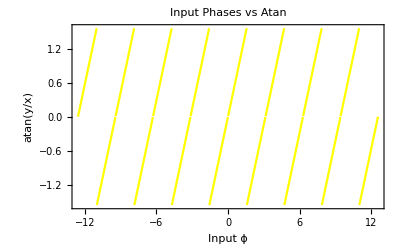

```mathematica
r = 1;
Phases =Plot[ArcTan[Im[r Exp[I phi]]/Re[r Exp[I phi]]],{phi,-4 Pi,4 Pi},PlotRange->All,PlotLabel->"Input Phases vs Atan",
Frame->True,
FrameLabel->{"Input ϕ","atan(y/x)"},
PlotStyle->Yellow]
```

```mathematica
Export["/home/nicolas/Documents/Programming/Computational Tools/01-Numerical_Errors/phases_m.pdf",Phases];
```

## 1.4 Subtractive Cancellation

Exploration of subtractive cancellation using the quadratic equation

```mathematica
a x^2 + b x + c = 1
```

and the different sets of solutions

```mathematica
Subscript[x, 1,2] = (-b ± √(b^2-4ac))/(2a),   Subscript[x', 1,2]=(-2c)/(b±√(b^2-4 a c))
```

```mathematica
a=1.;
b = 1.;
Nf=10;
x1[a_,b_,c_]:=(-b + Sqrt[b^2 - 4a c])/(2 a)
x2[a_,b_,c_]:=(-b - Sqrt[b^2 - 4a c])/(2 a)
xp1[a_,b_,c_]:=(2 c)/(b + Sqrt[b^2 - 4a c])
xp2[a_,b_,c_]:=(2 c)/(b - Sqrt[b^2 - 4a c])
Grid[Prepend[Table[
c=10^-n;
{n,SetPrecision[x1[a,b,c],15],SetPrecision[x2[a,b,c],15],
SetPrecision[xp1[a,b,c],15],SetPrecision[xp2[a,b,c],15]},{n,1,Nf}],
{"n","x_1","x_2","x'_1","x'_2"}],
Frame->All]
```

n | x_1 | x_2 | x'_1 | x'_2
1 | -0.112701665379258 | -0.887298334620742 | 0.112701665379258 | 0.887298334620742
2 | -0.0101020514433644 | -0.989897948556636 | 0.0101020514433644 | 0.989897948556633
3 | -0.00100100200501402 | -0.998998997994986 | 0.00100100200501404 | 0.99899899799501
4 | -0.000100010002000495 | -0.999899989997999 | 0.0001000100020005 | 0.999899989998055
5 | -0.0000100001000020167 | -0.999989999899998 | 0.0000100001000020001 | 0.999989999898335
6 | -1.00000100000663×10^-6 | -0.999998999999 | 1.000001000002×10^-6 | 0.999998999994366
7 | -1.00000009994883×10^-7 | -0.99999989999999 | 1.00000010000002×10^-7 | 0.999999900051182
8 | -1.00000001057587×10^-8 | -0.99999999 | 1.00000001×10^-8 | 0.999999989424126
9 | -1.00000002722922×10^-9 | -0.999999999 | 1.000000001×10^-9 | 0.999999972770781
10 | -1.00000008274037×10^-10 | -0.9999999999 | 1.0000000001×10^-10 | 0.999999917259636

## 1.5 Multiplicative Errors

Using the recursive relations (down), we are going to compute bessel functions

```mathematica
Subscript[j, n-1](x)=(2(n+1))/x Subscript[j, n](x) - Subscript[j, n+1](x)
```

```mathematica
x=1.;
L=24;
jn1 = SphericalBesselJ[L+1,x];
jn = SphericalBesselJ[L,x];
For[n=L,n≥ 0, n--,
j = (2n+1)/x jn - jn1;
jn1=jn;
jn = j;
ΔJ[n_,x_]:=Abs[j-SphericalBesselJ[n-1,x]];
Print[n,"\t",SetPrecision[j,15],"\t",SetPrecision[SphericalBesselJ[n-1,x],15],"\t",SetPrecision[ΔJ[n,x],15]]
]
```

24	8.30011891507678×10^-31	8.30011891507662×10^-31	1.59397700316948×10^-44

23	3.89936130991232×10^-29	3.89936130991228×10^-29	3.8675837615365×10^-43

22	1.75388257756904×10^-27	1.75388257756901×10^-27	2.36763388532321×10^-41

21	7.53779572223695×10^-26	7.53779572223688×10^-26	6.77286784165185×10^-40

20	3.08874236353958×10^-24	3.08874236353955×10^-24	2.93873587705572×10^-38

19	1.20385574220821×10^-22	1.2038557422082×10^-22	1.26953389888807×10^-36

18	4.45117750380685×10^-21	4.4511775038068×10^-21	4.51389830715758×10^-35

17	1.55670827059019×10^-19	1.55670827059017×10^-19	1.49259570690011×10^-33

16	5.13268611544381×10^-18	5.13268611544376×10^-18	5.16149225095779×10^-32

15	1.58957598751699×10^-16	1.58957598751698×10^-16	1.57772181044202×10^-30

14	4.60463767768383×10^-15	4.60463767768379×10^-15	4.73316543132607×10^-29

13	1.24166259698712×10^-13	1.24166259698711×10^-13	1.28742099732069×10^-27

12	3.09955185479011×10^-12	3.09955185479008×10^-12	3.19078458943795×10^-26

11	7.11655264004738×10^-11	7.11655264004731×10^-11	7.3670773305504×10^-25

10	1.49137650255516×10^-9	1.49137650255515×10^-9	1.46824558728162×10^-23

9	2.82649880221476×10^-8	2.82649880221473×10^-8	2.91167575618666×10^-22

8	4.79013419873954×10^-7	4.79013419873949×10^-7	4.87043944671223×10^-21

7	7.15693631008716×10^-6	7.15693631008708×10^-6	7.36918664111241×10^-20

6	0.0000925611586112591	0.0000925611586112582	9.21571846612679×10^-19

5	0.00101101580841376	0.00101101580841375	9.97465998686664×10^-18

4	0.00900658111711261	0.00900658111711252	8.84708972748172×10^-17

3	0.0620350520113745	0.0620350520113738	6.24500451351651×10^-16

2	0.30116867893976	0.301168678939757	2.99760216648792×10^-15

1	0.841470984807905	0.841470984807897	8.21565038222616×10^-15

0	0.540302305868145	0.54030230586814	5.32907051820075×10^-15

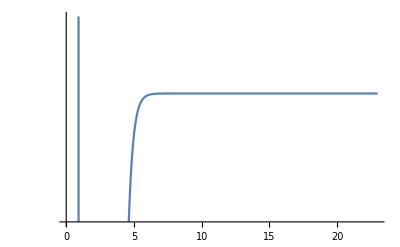

```mathematica
LogPlot[ΔJ[n,0.5],{n,0,23}]
```